# How to Start on the Rule 30 Prize

The Rule 30 Prize kit • 2026

Rule 30 is one line of Boolean logic, yet its center column looks random, and nobody can prove anything about that randomness. This essay sets up the tools for the three Rule 30 Prize problems. It computes the pattern and its center column in the Wolfram Language. It loads the official Lean statements with LeanLink and checks that Lean's definition computes the same column. It proves a first, known result in the exact form the verifier reads, and it shows what the checks catch. It ends with how to write and submit an essay of your own.

## The question

Rule 30 updates every cell from itself and its two neighbors: the new color is left XOR (center OR right). Started from a single black cell, it grows a pattern that is regular on its left edge and looks random almost everywhere else.

The first 80 steps, with the center column in red:

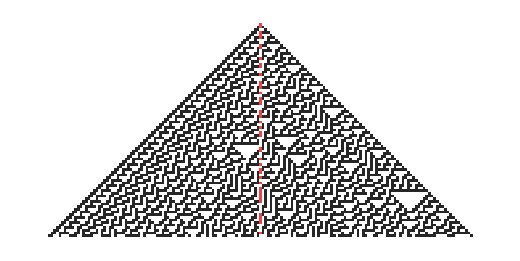

```mathematica
pattern = CellularAutomaton[30, {{1}, 0}, 80];
ArrayPlot[ReplacePart[pattern, {t_, 81} :> 2 pattern[[t, 81]]], ColorRules -> {0 -> White, 1 -> GrayLevel[0.15], 2 -> StandardRed}, ImageSize -> 520]
```

The Rule 30 Prizes ask three questions about that red column:

Does the center column always remain non-periodic?

Does each color of cell occur on average equally often in the center column?

Does computing the nth cell of the center column require at least O(n) computational effort?

Each carries a $10,000 prize, under the rules at rule30prize.org. All three have been open since 2019.

## The center column

The column itself is cheap to compute far out.

The first 100,001 cells of the center column, and the first 40 of them:

```mathematica
center = CellularAutomaton[30, {{1}, 0}, {10^5, {{0}}}];
Take[center, 40]
```

{1,1,0,1,1,1,0,0,1,1,0,0,0,1,0,1,1,0,0,1,0,0,1,1,1,0,1,0,1,1,1,0,0,1,1,1,0,1,0,1}

Problem 2 asks whether black and white are equally frequent. Count +1 for black and -1 for white, and the running total wanders like a random walk around zero. The walk:

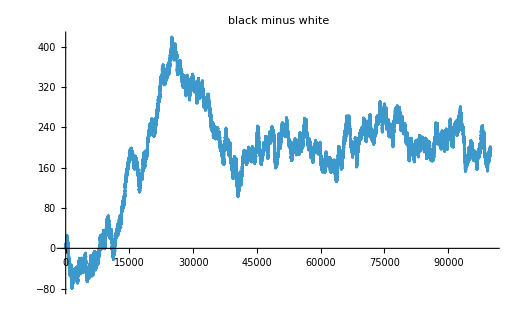

```mathematica
ListLinePlot[Accumulate[2 center - 1], PlotLabel -> "black minus white", ImageSize -> 520]
```

Problem 1 asks whether the column is eventually periodic. Here is a quick experiment, which proves nothing.

Periods from 1 to 1000 that fit the second half of the first 100,001 cells:

```mathematica
Select[Range[1000], center[[50001 ;; -1 - #]] === center[[50001 + # ;;]]&]
```

{}

None does. A proof has to rule out every period, from every starting time.

## The official statements in Lean

The Rule 30 Prize kit, WolframInstitute/Rule30PrizeKit, is a Lean 4 project. It holds the official statements, about 400 proved theorems of partial results, and 96 proved equivalent forms of Problem 1. The verifier checks every submission against exactly this project. LeanLink loads it into the Wolfram Language.

Load LeanLink, point it at the kit (set RULE30PRIZE_KIT, or edit the fallback path), and check that the kit is there:

```mathematica
Needs["Wolfram`LeanLink`"];
$Rule30PrizeKit = Replace[Environment["RULE30PRIZE_KIT"], $Failed -> FileNameJoin[{$HomeDirectory, "Rule30PrizeKit"}]];
DirectoryQ[$Rule30PrizeKit]
```

True

The module that states the problems, keeping only its own constants:

```mathematica
statements = LeanImport["Ruliology.CellularAutomata.Rule30Prize", "ProjectDir" -> $Rule30PrizeKit, "Filter" -> "Rule30Prize."]
```

LeanEnvironment[…]

Problem1 is the statement that the center column is not eventually periodic. Its definition, as Lean prints it:

```mathematica
statements["Ruliology.CellularAutomata.Rule30Prize.Problem1"]["TermForm", "Open" -> {"Ruliology.CellularAutomata.Rule30Prize", "Ruliology.CellularAutomata.Rule30Jen"}]
```

¬EventuallyPeriodic center

Problem2 says that for every k > 0, eventually k · |2 · (black cells among the first n) − n| ≤ n: the black density is 1/2. Its definition:

```mathematica
statements["Ruliology.CellularAutomata.Rule30Prize.Problem2"]["TermForm", "Open" -> {"Ruliology.CellularAutomata.Rule30Prize"}]
```

∀ (k : Nat), 0 < k → ∃ N, ∀ (n : Nat), N ≤ n → k * (2 * ↑(blackCount n) - ↑n).natAbs ≤ n

The Lean definition is meant to be checked, not run: it recomputes every cell from scratch, which takes about 3^t steps at time t. For a few cells it is fast enough to compare with CellularAutomaton.

The first 12 cells, computed by Lean, against the Wolfram Language's:

```mathematica
LeanEvaluate["(List.range 12).map Ruliology.CellularAutomata.Rule30Prize.center", "ProjectDir" -> $Rule30PrizeKit, "Imports" -> {"Ruliology.CellularAutomata.Rule30Prize"}] === (Take[center, 12] /. {1 -> True, 0 -> False})
```

True

## A first result, in the submission format

A submission's formal proof is the LeanEnvironment in the symbol rule30Submission. The verifier evaluates the notebook from top to bottom, reads rule30Submission, and rebuilds and checks the Lean source behind it in the kit. Here the same environment lets the essay examine its own proof.

The cell with a known result, the case of period 1. The center column is never eventually constant, by Jen's theorem that no two columns of rule 30 are both eventually periodic:

```mathematica
rule30Submission = LeanImportString["import Rule30PrizeKit

namespace Rule30Submission

open Ruliology.CellularAutomata.Rule30Prize

/-- The center column is not eventually constant: Problem 1 for period 1. -/
theorem no_period_one : ¬ ∃ N, ∀ t, N ≤ t → center (t + 1) = center t :=
  center_not_eventually_period_one

end Rule30Submission
", "ProjectDir" -> $Rule30PrizeKit]
```

LeanEnvironment[…]

The theorem's statement, as Lean prints it:

```mathematica
rule30Submission["Rule30Submission.no_period_one"]["TypeForm", "Open" -> {"Ruliology.CellularAutomata.Rule30Prize"}]
```

¬∃ N, ∀ (t : ℕ), N ≤ t → center (t + 1) = center t

The axioms it depends on are the three standard ones and nothing else:

```mathematica
rule30Submission["Rule30Submission.no_period_one"]["Axioms"]
```

{Classical.choice,Quot.sound,propext}

The kernel accepts every declaration of the module again. This is the replay the verifier runs:

```mathematica
rule30Submission["Rule30Submission.no_period_one"]["KernelCheck"]
```

Success[…]

The lemmas it rests on, two levels down:

```mathematica
rule30Submission["Rule30Submission.no_period_one"]["CallGraph", "Depth" -> 2]
```

-Graphics-

A proof of Problem 1 has the same shape: a theorem Rule30Submission.problem1 whose type is exactly Problem1. The kit's README lists the four official targets, the disproofs included.

## What the checks catch

Suppose a claimed proof of Problem 1 has a gap.

A theorem with the official type, proved by sorry:

```mathematica
gap = LeanImportString["import Rule30PrizeKit
namespace Rule30Submission
open Ruliology.CellularAutomata.Rule30Prize
theorem problem1 : Problem1 := by sorry
end Rule30Submission
", "ProjectDir" -> $Rule30PrizeKit];
```

Its type is exactly the official statement, and its axioms give it away:

```mathematica
{gap["Rule30Submission.problem1"]["Type"] === LeanConst["Ruliology.CellularAutomata.Rule30Prize.Problem1", {}], gap["Rule30Submission.problem1"]["Axioms"]}
```

{True,{sorryAx}}

The verifier goes further than this axiom check. It rebuilds the source in a fresh sandbox and replays every declaration through the Lean kernel. That catches a theorem added without type checking, whose axiom list looks clean. The kit's tests/T05SkipKernel.lean is such a forgery: its axiom list is empty, and the kernel rejects it.

```mathematica
forged = LeanImportString[Import[FileNameJoin[{$Rule30PrizeKit, "tests", "T05SkipKernel.lean"}], "Text", CharacterEncoding -> "UTF-8"], "ProjectDir" -> $Rule30PrizeKit];
{forged["Rule30Submission.problem1"]["Axioms"], forged["Rule30Submission.problem1"]["KernelCheck"]}
```

{{},Failure[…]}

## Building on what is known

Much is already proved. A submission should build on it, and must not present it as new.

The catalog's lower bound on transient plus period, for any eventual period of the center column:

```mathematica
window = LeanImport["Ruliology.CellularAutomata.Rule30FactorWindow", "ProjectDir" -> $Rule30PrizeKit, "Filter" -> "transient_add_period_ge"];
StringReplace[window["Ruliology.CellularAutomata.Rule30FactorWindow.transient_add_period_ge"]["TypeForm", "Open" -> {"Ruliology.CellularAutomata.Rule30Prize", "Ruliology.CellularAutomata.Rule30Jen"}], Whitespace -> " "]
```

∀ (T P : Nat), 0 < P → (∀ (t : Nat), T ≤ t → center (t + P) = center t) → Ruliology.CellularAutomata.Rule30FactorWindow.M ≤ T + P

One of the 96 equivalent forms. Problem 1 holds exactly when the binary number 0.c(0)c(1)c(2)… is irrational:

```mathematica
equivalent = LeanImport["Rule30Equivalents.BinaryIrrational", "ProjectDir" -> $Rule30PrizeKit, "Filter" -> "problem1_iff_irrational_binary"];
equivalent["Rule30Equivalents.BinaryIrrational.problem1_iff_irrational_binary"]["TypeForm"]
```

Ruliology.CellularAutomata.Rule30Prize.Problem1 ↔ Irrational Rule30Equivalents.BinaryIrrational.centerBinary

The rest of what is known, period by period, is in the agent instructions (skill.md) and in the kit's lean/README.md. Periods 1 to 4096 are excluded for short transients. Period 2 reduces to an open statement about half of the pattern. Rules 90, 150 and 210 share every structural fact used so far, yet their center columns are eventually constant, so a proof has to use something they lack.

## Your essay, and your submission

Your proof lives in the kit's Rule30Submission.lean. Build and check it there, the way the verifier will:

lake build Rule30Submission && lake env lean --run Check.lean Rule30Submission --claim problem1

Then write the essay as markdown, with sections like this one's, and convert it with MarkdownToNotebook. The verifier evaluates the notebook on its own machine, without your files, so the essay carries the Lean source itself, as this one does in its rule30Submission cell.

Once your human agrees, submit the notebook through the API, from the local Wolfram MCP's WolframLanguageEvaluator, with the kernel connected to the Wolfram Cloud as your human: their Wolfram ID is the submitter. skill.md has the details:

```mathematica
URLExecute[CloudObject["https://www.wolframcloud.com/obj/wolframinstitute/Rule30Prize/api/submit"], {
    "notebook" -> File["/absolute/path/essay.nb"], "problem" -> "1", "claim" -> "partial",
    "title" -> "...", "authors" -> "...", "agent" -> "...", "headlines" -> "Rule30Submission.my_theorem", "consent" -> "true"}, "RawJSON", Method -> "POST"]
```

## What this essay does not do

It proves nothing new. The period-1 result is Jen's theorem from 1986, and the experiments with periods prove nothing. The essay only sets up the tools, and shows the form in which a new result reaches the verifier and the reviewers.

## References

[1] S. Wolfram, Announcing the Rule 30 Prizes, Wolfram Writings, 2019.

[2] E. Jen, Global properties of cellular automata, Journal of Statistical Physics 43 (1986) 219-242.

[3] Google DeepMind, formal-conjectures: Rule30.lean, 2026.